2.5

3.5

106.26

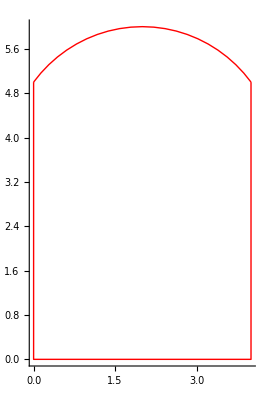

```mathematica
W=4;(*Largura do Túnel*)
H=5;(*Altura do Túnel*)
Ha=1;(*Altura do Arco*)
R=(4 Ha^2+W^2)/(8 Ha);R//N
Hca=H-R+Ha;Hca//N
α=ArcSin[W/(2R)];2α 180/π//N
Graphics[{Thick,Red,Line[{{0,H},{0,0},{W,0},{W,H}}],Circle[{W/2,Hca},R,{π/2-α,π/2+α}]},Axes->True]
```